MACHINE LEARNING EXAMPLES

I. Predict survival of Titanic passengers

```mathematica
dataset=ExampleData[{"MachineLearning","Titanic"},"Data"]; (* data are downloaded @ 'C:\Users\Soutrik\AppData\Roaming\Mathematica\Paclets\Repository\' folders *)
c=Classify[dataset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

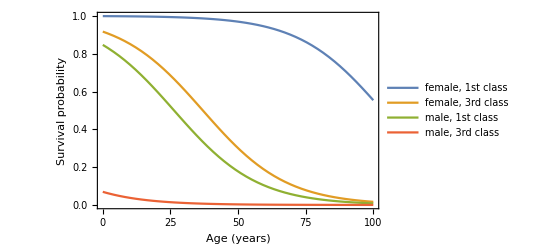

```mathematica
p[class_,age_,sex_]:=c[{class,age,sex},{"Probability","survived"}];
Plot[{p["1st",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["3rd",x,"male"]},{x,0,100},PlotLegends->{"female, 1st class","female, 3rd class","male, 1st class","male, 3rd class"},Frame->True,FrameLabel->{"Age (years)","Survival probability"}]
```

II. Predictor performance of Boston housing

```mathematica
p=Predict[ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"],PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,ExampleData[{"MachineLearning","BostonHomes"},"TestData"]]
```

PredictorMeasurementsObject[…]

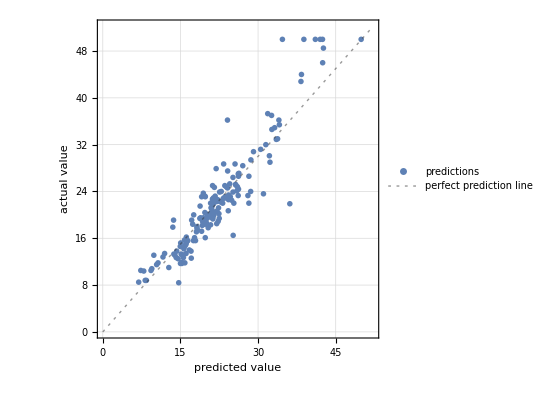

```mathematica
pm["ComparisonPlot"]
```

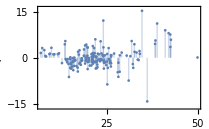

```mathematica
pm["ResidualPlot"]
```

```mathematica
pm["StandardDeviation"]
```

3.39613

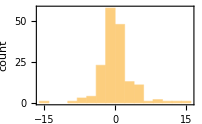

```mathematica
pm["ResidualHistogram"]
```

III. Confusion matrix visualisation of a classifier

```mathematica
trainingset=ExampleData[{"MachineLearning","Satellite"},"TrainingData"];
testset=ExampleData[{"MachineLearning","Satellite"},"TestData"];
```

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[c,testset]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.8875

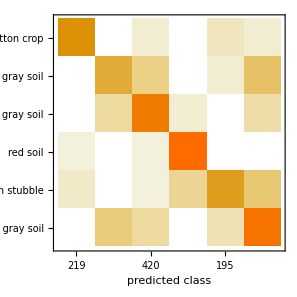

```mathematica
cm["ConfusionMatrixPlot"]
```

IV. Forecast temperatures

```mathematica
dataset={#2,ToExpression[#3],#4}->#1&@@@ExampleData[{"Statistics","USCityTemperature"}];
```

```mathematica
p=Predict[dataset,Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
months={"January","February","March","April","May","June","July","August","September","October","November","December"};
distributions=MapIndexed[{First[#2],p[{"Lincoln",2020,#1},"Distribution"]}&,months];
```

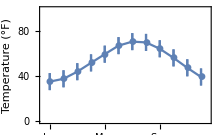

```mathematica
Needs["ErrorBarPlots`"]
ErrorListPlot[{{#1,Mean[#2]},ErrorBar[StandardDeviation[#2]]}&@@@distributions,FrameTicks->{{Automatic,None},{Transpose[{Range[12],Rotate[StringTake[#,3],Pi/3]&/@months}],None}},PlotMarkers->Automatic,Frame->True,Joined->True,PlotRange->{{.5,12.5},{0,100}},FrameLabel->{None,"Temperature (°F)"},LabelStyle->14]
```

V. MNIST data of handwritten digits

```mathematica
digit = Classify[
  {-Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 9, -Graphics- -> 6, -Graphics- -> 2, -Graphics- -> 8, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 6, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 7, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 6, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 1, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 9, -Graphics- -> 6}]
```

ClassifierFunction[…]

```mathematica
digit[-Graphics-, "TopProbabilities"]
```

{4→0.375915,6→0.354657,0→0.235305}

VI. Visualise the probability distributions of classifier

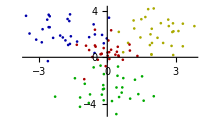

```mathematica
sampledata[center_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],30];
clusters=sampledata/@{{2,2},{-2,2},{0,-3},{0,-0}};
colors={Yellow,Blue,Green,Red};
ListPlot[clusters,PlotStyle->Darker@colors]
```

```mathematica
plotprobabilities[method_]:=Module[{c,proba},c=Classify[<|Thread[colors->clusters]|>,Method->method];
proba=Table[Append[{x,y},#]&/@Lookup[c[{x,y},"Probabilities"],colors],{x,-4,4,.5},{y,-5,4,.5}];
proba=Flatten[#,1]&/@Transpose[proba,{3,2,1,4}];
Show[ListPlot3D[proba,PlotRange->{0,1},PlotLabel->method],ListPointPlot3D[Map[Append[#,1]&,clusters,{2}],PlotStyle->({Opacity[0.5],#}&/@colors)]]];
plotprobabilities/@{"LogisticRegression","NearestNeighbors","RandomForest","SupportVectorMachine","NaiveBayes","NeuralNetwork"}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

BASIC DATA ANALYSIS WITH MATHEMATICA

```mathematica
(* Edgar Anderson's Iris data *)
iris=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data"];
iris=Delete[iris, Length[iris]];
props={"SepalLength","SepalWidth","PetalLength","PetalWidth","Species"};
data=Association[MapIndexed[(First[props[[#2]]]-> #1)&,Transpose[iris]]];
dataset=Dataset[data]
```

Dataset[<>]

```mathematica
sepalLength=Normal[dataset[["SepalLength"]]];
```

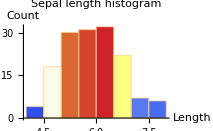

```mathematica
Histogram[sepalLength,ColorFunction->ColorData["Temperature"],AxesLabel->{"Length","Count"},PlotLabel->"Sepal length histogram",LabelStyle->{GrayLevel[0]}]
```

```mathematica
sepDist=HistogramDistribution[sepalLength];
```

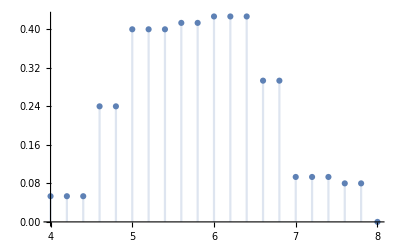
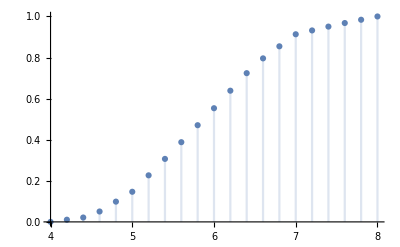

```mathematica
{DiscretePlot[PDF[sepDist,x],{x,4,8,0.2}],DiscretePlot[CDF[sepDist,x],{x,4,8,0.2}]}
```

```mathematica
StandardDeviation[sepalLength]
```

0.828066

```mathematica
sepDist=EmpiricalDistribution[sepalLength];
```

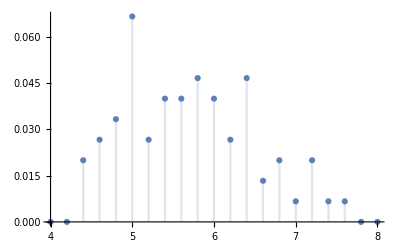
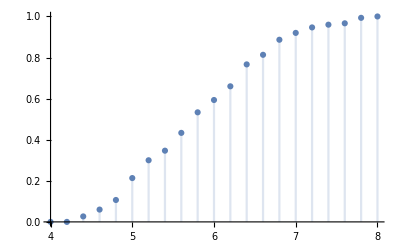

```mathematica
{DiscretePlot[PDF[sepDist,x],{x,4,8,0.2}],DiscretePlot[CDF[sepDist,x],{x,4,8,0.2}]}
```

```mathematica
estSepDist=EstimatedDistribution[sepalLength,GammaDistribution[α,β]];
```

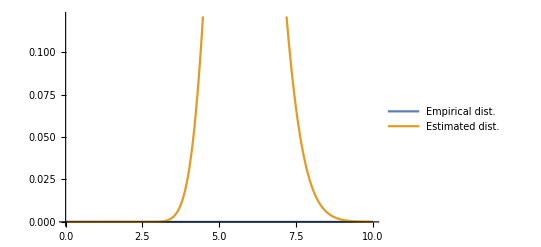

```mathematica
Plot[{PDF[sepDist,x],PDF[estSepDist,x]},{x,0,10},PlotLegends->{"Empirical dist.","Estimated dist."}]
```

```mathematica
FindDistributionParameters[sepalLength,LaplaceDistribution[μ,σ]]
```

{μ→5.8,σ→0.684667}

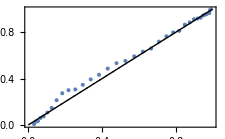

```mathematica
ProbabilityPlot[sepalLength]
```

```mathematica
sepal=Thread[{data[[1]],data[[2]]}];
```

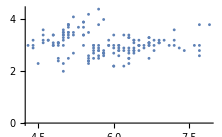

```mathematica
ListPlot[sepal]
```

```mathematica
species=Map[(#[[1;;2]])&,Values[GroupBy[sepal,Last]],{2}];
```

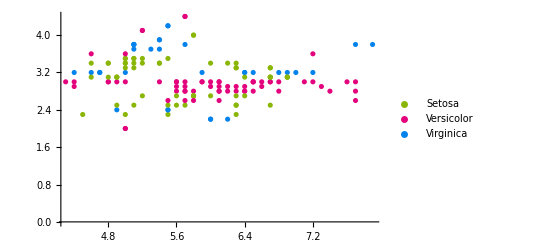

```mathematica
ListPlot[species,PlotStyle->{ColorData[3][4],ColorData[3][9],ColorData[3][6]},PlotLegends->{"Setosa","Versicolor","Virginica"}]
```

```mathematica
clusters=FindClusters[Flatten[species,1],3];
```

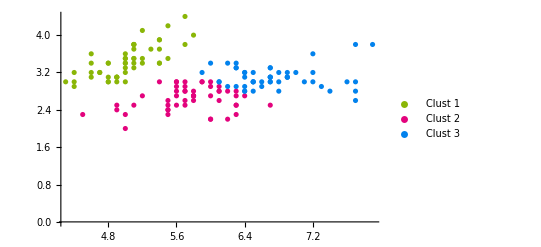

```mathematica
ListPlot[clusters,PlotStyle->{ColorData[3][4],ColorData[3][9],ColorData[3][6]},PlotLegends->{"Clust 1","Clust 2","Clust 3"}]
```

```mathematica
classificationMap=Flatten[Map[(#[[1;;2]]-> #[[3]])&,Values[GroupBy[sepal,Last]],{2}],1];
classify = Classify[classificationMap]
```

Part::partw: Part 3 of {5.1,3.5} does not exist.

Part::partw: Part 3 of {5.2,3.5} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ClassifierFunction[…]

```mathematica
classify[{{5,4},{6.2,3}}]
```

{{5.1,3.8}⟦3⟧,{6.1,3.}⟦3⟧}

```mathematica
predictMap=Flatten[Map[({#[[1]],#[[3]]}->#[[2]])&,Values[GroupBy[sepal,Last]],{2}],1];
predict = Predict[predictMap,NominalVariables->{2}]
```

Part::partw: Part 3 of {5.1,3.5} does not exist.

Part::partw: Part 3 of {5.2,3.5} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Predict::mlnomvar: Inactive option NominalVariables. Use FeatureTypes instead.

PredictorFunction[…]

```mathematica
predict[{4.5,"Iris-setosa"}]
```

3.09199

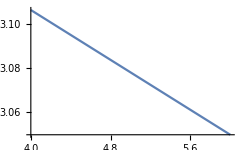

```mathematica
Plot[predict[{x,"Iris-setosa"}],{x,4,6}]
```

```mathematica
PredictorInformation[predict,"Properties"]
```

{ExampleNumber,ExtractedFeatureNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,MaxTrainingMemory,Method,MethodDescription,PerformanceGoal,Properties,TrainingTime,UtilityFunction}

```mathematica
PredictorInformation[predict,"DistributionFunction"]
```

PredictorInformation::mlnaset: DistributionFunction is not an available Property.

PredictorInformation[PredictorFunction[…],DistributionFunction]

MATHEMATICA FOR PREDICTION

I. Import antononcube packages

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MosaicPlot.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/RSparseMatrix.m"]
```

II. Titanic data

```mathematica
titanicData=Flatten@*List@@@ExampleData[{"MachineLearning","Titanic"},"Data"];
titanicData=DeleteCases[titanicData,{___,_Missing,___}];

titanicColumnNames=Flatten@*List@@ExampleData[{"MachineLearning","Titanic"},"VariableDescriptions"];
aTitanicColumnNames=AssociationThread[titanicColumnNames->Range[Length[titanicColumnNames]]];
```

```mathematica
Dimensions[titanicData]
RecordsSummary[titanicData,titanicColumnNames]
```

{1046,4}

{1 passenger class
3rd | 501
1st | 284
2nd | 261,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.8811
3rd Qu | 39.
Max | 80.,3 passenger sex
male | 658
female | 388,4 passenger survival
died | 619
survived | 427}

III. Install R

```mathematica
Needs["RLink`"]
RLinkResourcesInstall[]
InstallR[]
```

{Paclet[RLinkRuntime,9.0.0.0,<>]}

IV. Mosaic plot

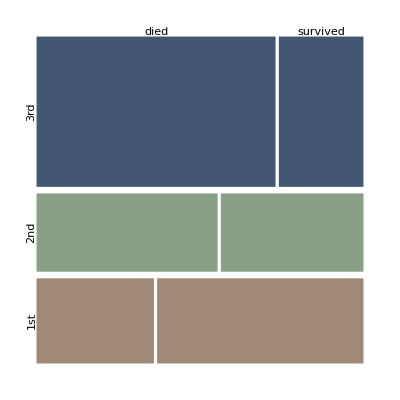

```mathematica
MosaicPlot[titanicData[[All,aTitanicColumnNames/@{"passenger class","passenger survival"}]]]
```

INFECTIOUS DISEASE MODEL - INFLUENZA

I. SIR MODEL

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Manipulate[
DynamicModule[{s0,r0,α,sol,s,i,r,t},
s0=1−i0;r0=0;α=1/l;
sol=NDSolve[
{s'[t]==−β*s[t]*i[t],
i'[t]==β*s[t]*i[t]−α*i[t],
r'[t]==α*i[t],
s[0]==s0,i[0]==i0,r[0]==r0},{s,i,r},{t,0,150}];
Plot[{s[t]/.sol,i[t]/.sol,r[t]/.sol},
{t,0,30},PlotStyle->{Darker[Green],Red,Blue},
PlotRange->{0,1},PlotLegend->{"S","I","R"},
LegendPosition->{0.5,−0.2},LegendShadow->None,ShadowBorder->None,
FrameLabel->{Style["time (in days)",Medium],Style[" ",Medium]},
Frame->{{True,False},{True,False}}]
],
{{i0,0.001,"I0: infected at the beginning"},0,0.1,0.001,ImageSize->Tiny,Appearance->"Labeled"},
{{β,1.5,"β: transmission rate"},0.5,5,0.5,ImageSize->Tiny,Appearance->"Labeled"},
{{l,3,"1/α: infectious period (in days)"},1,7,1,ImageSize->Tiny,Appearance->"Labeled"}
]
```